```mathematica
Remove["Global`*"];
```

## Setting Cosmological History

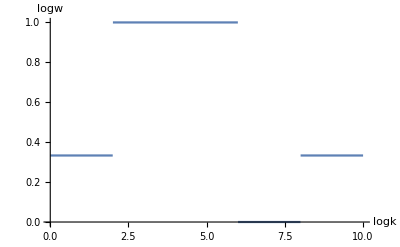

```mathematica
w=Piecewise[{{1,logk>2&&logk<6},{0,logk>6&&logk<8}},1/3];
beta=-2(1-3*w)/(1+3*w);
Plot[w,{logk,0,10},AxesLabel->{logk,logw}]
```

## Gaussian input in Log scale

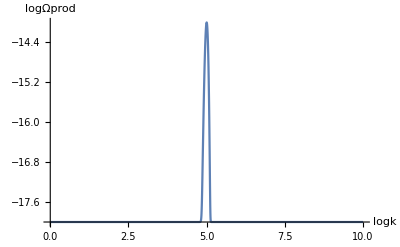

```mathematica
init=Log[10,(10^(-18)*(1+10000*Exp[-((10^logk-100000)/10000)^2]))];
Plot[init,{logk,0,10},AxesLabel->{logk,logΩprod}]
```

## Derivative and Addition

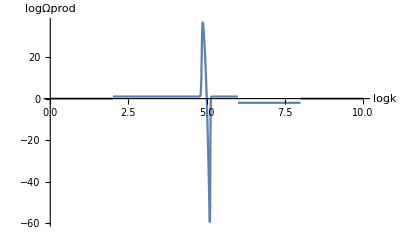

```mathematica
deriv=D[init,logk];
kernel=N[deriv+beta];
Plot[kernel,{logk,0,10},AxesLabel->{logk,logΩprod},PlotRange->Full]
```

## Integration and Plotting

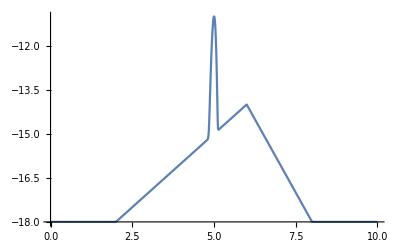

```mathematica
Plot[(NIntegrate[kernel,{logk,0,x}]-18),{x,0,10},PlotRange->Full]
```